# Curved rod

```mathematica
$Assumptions = _ ∈ Reals;
```

## Semiclassical analysis

```mathematica
(*  Finds a quantized orbit near another (approximately quantized) 
		orbit by minimizing the estimated quantum number.  *)
quantize[m_, dm_, mInv_, ω_?NumericQ, ϵ_?NumericQ, δ:(_?NumericQ):0.01, OptionsPattern[]] := Module[
	{t, x, k, eqs, actionIntegral, nEst, ωEst, n, ωGuess, res},
	
	(*  Set up all equations except x[0], which would depend on ω,
			which is the quantity we want to optimize.  *)
	eqs = {
		x'[t] == k[t](2 k[t]^2 + 1 + ((2 k[t]^2 + 1)(k[t]^4 + k[t]^2 + m[x[t]]^2) - 6 k[t]^4)/(√((k[t]^4 - k[t]^2 + m[x[t]]^2)^2 + 4 k[t]^2 m[x[t]]^2))), 
		k'[t] == -m[x[t]]dm[x[t]](1 + (k[t]^4 + k[t]^2 + m[x[t]]^2)/(√((k[t]^4 - k[t]^2 + m[x[t]]^2)^2 + 4 k[t]^2 m[x[t]]^2))),
		k[0] == 0,
		
		(*  Ensure that we stop the integration once we reach the turning 
				point on the positive x axis.  We will always start the integration 
				from the turning point on the negative x axis.  *)
		WhenEvent[k[t] == 0 && t > 0, "StopIntegration"]
	};
	
	actionIntegral[eqs_] := (
		(*  We should ideally be using a sympletic integrator.  *)
		sol = NDSolve[eqs, {x, k}, {t, 0, ∞}];
		
		(*  Use the undocumented "Domain" method of InterpolatingFunction
				to get the the time at which we hit the next turning point.  *)
		NIntegrate[k[t]D[x[t], t]/.First@sol, {t}~Join~(First@(x/.First@sol)["Domain"])]
	);
	
	(*  Roughly estimate the quantum number n.  *)
	nEst[ωEst_?NumericQ] := actionIntegral[eqs~Join~{x[0] == mInv[ωEst]}]/(ϵ π) - 0.5;
	n = Round[nEst[ω]];
	
	If[OptionValue["RandMin"],
		ωGuess = RandomReal[{Max[ω - δ, m[0]], Min[ω + δ, m[∞]]}, OptionValue["NRand"]];
		res = (nEst[#] - n)^2 & /@ ωGuess;
		ωGuess = ωGuess[[Ordering[res, 1]]][[1]];
		{Round[nEst[ωGuess]], ωGuess, Min[res]},
		res = ωEst/.FindRoot[nEst[ωEst] - n, {ωEst, ω}];
		{n, res, Abs[(nEst[res] - n)]/(n + 10^-1)}
	]
];

Options[quantize] = {"RandMin"->False, "NRand"->10};
```

## Quantization

### sech-type curvature

```mathematica
m[x_]:=0.1-(0.1-0.01)Sech[x];
dm[x_]:=(0.1-0.01)Sech[x]Tanh[x];
mInv[ω_?NumericQ] := -ArcSech[(0.1-ω)/(0.1-0.01)];
```

```mathematica
ωSpectral = (Transpose@Import["~/code/glwtes/rod/data/sech_bc_cc_b0.1_a0.01_N_2048/quantized.txt","Table"])[[1]]
```

{0.0214624,0.0351925,0.0456192,0.0540572,0.0611555,0.0672413,0.0725181,0.0771239,0.0811552,0.0846803,0.08775,0.0904067,0.0926887,0.094626,0.0962381,0.0975419,0.0985579,0.0992977}

```mathematica
ωQuantize=ParallelMap[quantize[m,dm,mInv,#,0.01]&,ωSpectral];
```

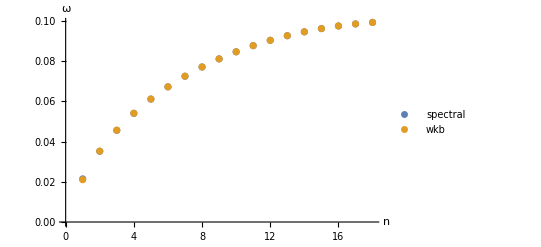

```mathematica
ListPlot[{ωSpectral,ωQuantize[[All,2]]},AxesLabel->{"n", "ω"},PlotLegends->{"spectral", "wkb"}]
```

```mathematica
Export["~/code/glwtes/rod/data/sech_bc_cc_b0.1_a0.01_N_2048/wkb.txt",ωQuantize,"Table"];
```

### Tanh-type curvature

```mathematica
m[x_]:=0.1Tanh[x];
dm[x_]:=0.1 Sech[x]^2;
mInv[ω_?NumericQ] := -ArcTanh[ω/0.1];
```

```mathematica
ωSpectral = (Transpose@Import["~/code/glwtes/rod/data/tanh_bc_cc_b0.1_N_2048/quantized.txt","Table"])[[1]]
```

{0.0308561,0.052484,0.0660214,0.0759116,0.0834561,0.0892568,0.0936448,0.0968089,0.0988595,0.0998722}

```mathematica
ωQuantize=ParallelMap[quantize[m,dm,mInv,#,0.01]&,ωSpectral];
```

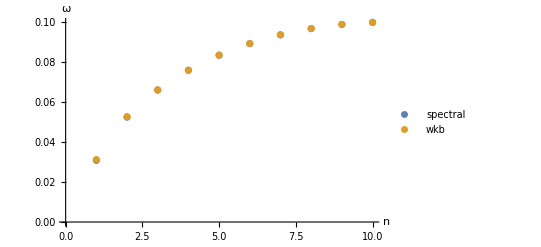

```mathematica
ListPlot[{ωSpectral,ωQuantize[[All,2]]},AxesLabel->{"n", "ω"},PlotLegends->{"spectral", "wkb"}]
```

```mathematica
Export["~/code/glwtes/rod/data/tanh_bc_cc_b0.1_N_2048/wkb.txt",ωQuantize,"Table"];
```

## Miscellaneous

Find k for a given ω and m so that we can star the ray tracing on the k axis.

```mathematica
omega2k[ω_,m_]:=Select[k/.Solve[1/2(k^2+k^4+m^2+√((k^2-k^4-m^2)^2+4 k^2 m^2))==ω^2,k],(#∈ Reals && # >0)& ][[1]]
```

#### Tanh-type

```mathematica
ω={0.030858579,0.052487037,0.066021797,0.075910417,0.083455045,0.089256940,0.093645579,0.096808817,0.098859160,0.099878743};
omega2k[#,0]&/@ω
```

{0.0308586,0.052487,0.0660218,0.0759104,0.083455,0.0892569,0.0936456,0.0968088,0.0988592,0.0998787}

#### Sech-type

```mathematica
ω={0.021460271,0.035192708,0.045620597,0.054058048,0.061155004,0.067240133,0.072517533,0.077124418,0.081156171,0.084680547,0.087749200,0.090406118,0.092689236,0.094626586,0.096237486};
```

```mathematica
omega2k[#,0.01]&/@ω
```

{0.0189872,0.0337405,0.044509,0.0531225,0.0603289,0.0664891,0.0718212,0.0764696,0.0805337,0.0840838,0.0871732,0.0898469,0.0921436,0.094092,0.0957118}